# Measurement of Total Pauli Z

Here, a quantum circuit implementation is introduced to measure the total Pauli Z, that is, Z_tot:=Z_1+Z_2+…Z_n, where Z_k is the Pauli Z operator acting on the k^th qubit.

Make sure that Q3 is loaded.

```mathematica
<<Q3`
```

Let us consider a system of n qubits.

```mathematica
$n=5;
$l=Ceiling@Log[2,$n+1];
```

We want to measure S_tot^z:=S_1^z+S_2^z+…+S_n^z. The auxiliary register T is used to store the result.

```mathematica
Let[Qubit,S,T]
SS=S[Range@$n,None];
TT=T[Range@$l,None];
```

This is a short-cut function:  addBitValue[p] generates the quantum circuit elements to add the bit value of qubit p.

```mathematica
Clear[addBitValue];addBitValue[]:=Sequence@@Table[addBitValue[p],{p,$n}]
addBitValue[p_]:=Sequence@@With[
{logp=Ceiling@Log[2,p+1]},
Table[CNOT[Prepend[T@Range[k-1],S[p]],T[k]],{k,logp,1,-1}]
]
```

This copies the value of the first qubit.

```mathematica
QuantumCircuit[
Ket[TT],
addBitValue[1],
"Visible"->SS,
"Invisible"->S[$n+1/2]
]
```

-Graphics-

Then, the value of the second qubit is added. Note that the second qubit in the ancillary register plays the role of carrier bit.

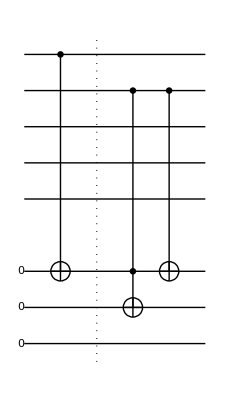

```mathematica
QuantumCircuit[
Ket[TT],
addBitValue[1],"Separator",
addBitValue[2],
"Visible"->SS,
"Invisible"->S[$n+1/2]
]
```

We repeat the same procedure for the third qubit. Note here that the third qubit is not necessary at this stage because the maximum value of the sum of the values of three qubits is 3.

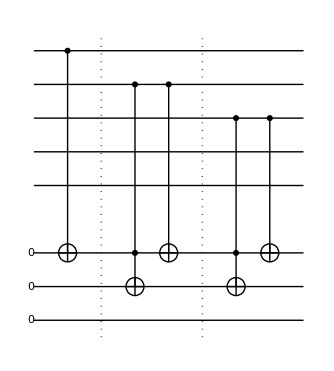

```mathematica
QuantumCircuit[
Ket[TT],
addBitValue[1],"Separator",
addBitValue[2],"Separator",
addBitValue[3],
"Visible"->SS,
"Invisible"->S[$n+1/2]
]
```

We repeat the same procedure, but now we need additional carrier bit (the third) in the ancillary register.

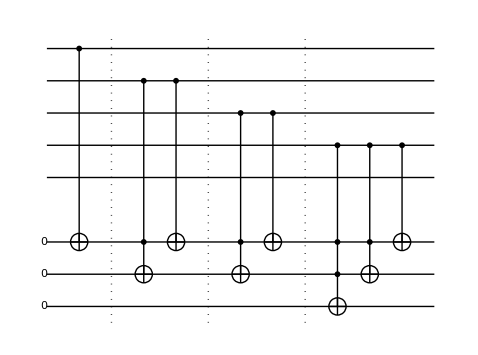

```mathematica
QuantumCircuit[
Ket[TT],
addBitValue[1],"Separator",
addBitValue[2],"Separator",
addBitValue[3],"Separator",
addBitValue[4],
"Visible"->SS,
"Invisible"->S[$n+1/2]
]
```

Putting all together, the following quantum circuit can measure the sum of the values of all qubits in the native register.

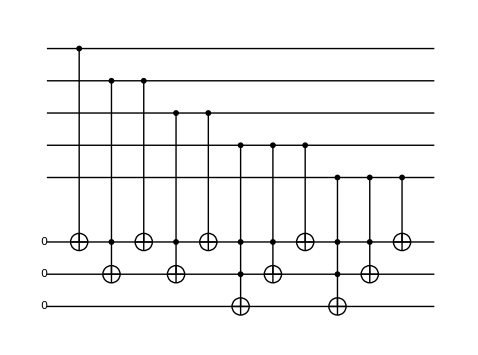

```mathematica
qc=QuantumCircuit[Ket[TT],addBitValue[],"Invisible"->S[$n+1/2]]
```

Let us check that the above quantum circuit indeed generates the correct value in the ancillary register.

```mathematica
bs=Basis[SS];
```

```mathematica
Timing[out=qc**bs;]
```

{1.38584,Null}

Extracts the sum from the output state in the ancillary register. In actual situation, one should perform the measurement on the ancillary register in the computation basis.

```mathematica
num=FromDigits[#,2]&/@Reverse/@Through[out[TT]]
```

{0,1,1,2,1,2,2,3,1,2,2,3,2,3,3,4,1,2,2,3,2,3,3,4,2,3,3,4,3,4,4,5}

Compare the input state and the sum.

```mathematica
Thread[SimpleForm[bs]->num]//TableForm
```

00000→0
00001→1
00010→1
00011→2
00100→1
00101→2
00110→2
00111→3
01000→1
01001→2
01010→2
01011→3
01100→2
01101→3
01110→3
01111→4
10000→1
10001→2
10010→2
10011→3
10100→2
10101→3
10110→3
10111→4
11000→2
11001→3
11010→3
11011→4
11100→3
11101→4
11110→4
11111→5

```mathematica
OccupationValue[SS,1]/@bs-num
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Related Guides

Quantum Information Systems

Quantum Many-Body Systems

Quantum Spin Systems

Related Tech Notes

Addition of Numbers

A Quantum Playbook

Quantum Information Systems with Q3

Quantum Many-Body Systems with Q3

Quantum Spin Systems with Q3

Related Links

V. Vedral, A. Barenco and A. Ekert, Physical Review A 54, 147 (1996), “Quantum networks for elementary arithmetic operations.”

Mahn-Soo Choi (2022), A Quantum Computation Workbook (Springer, 2022).

## Metadata

### Categorization

Tech Note

QuantumPlaybook

QuantumPlaybook`

QuantumPlaybook/tutorial/MeasurementOfTotalPauliZ

### Keywords